```mathematica
a=π^-1/10
```

1/(10 π)

```mathematica
N[a]
```

0.031831

0.31831

```mathematica
Table[∫_(i-1)^i 4 π^-0.5 N[a]^3 ⅇ^(-N[a]^2 x^2)x^2 ⅆx,{i,321}]
```

{0.0000242466,0.000169373,0.000457864,0.000886225,0.00144928,0.00214025,0.00295085,0.00387142,0.00489107,0.00599783,0.00717883,0.00842048,0.00970868,0.011029,0.0123668,0.0137078,0.0150375,0.0163422,0.0176086,0.0188245,0.0199781,0.021059,0.0220577,0.0229661,0.0237771,0.0244853,0.0250862,0.0255769,0.0259556,0.0262219,0.0263767,0.0264217,0.0263601,0.0261958,0.0259335,0.0255788,0.025138,0.0246178,0.0240254,0.0233682,0.0226539,0.0218903,0.0210851,0.020246,0.0193804,0.0184956,0.0175985,0.0166955,0.0157928,0.014896,0.0140103,0.0131402,0.0122899,0.0114631,0.0106628,0.00989166,0.00915175,0.00844476,0.00777192,0.00713403,0.00653155,0.00596459,0.00543295,0.00493614,0.00447347,0.00404402,0.00364669,0.00328026,0.00294339,0.00263464,0.00235254,0.00209554,0.00186211,0.00165071,0.0014598,0.0012879,0.00113354,0.000995322,0.000871899,0.000761987,0.000664372,0.000577912,0.000501535,0.000434243,0.000375111,0.000323285,0.00027798,0.000238476,0.000204118,0.000174313,0.000148521,0.000126258,0.00010709,0.0000906268,0.0000765217,0.0000644667,0.000054189,0.0000454479,0.0000380317,0.0000317547,0.0000264546,0.0000219902,0.0000182387,0.0000150937,0.0000124634,0.0000102687,8.44191×10^-6,6.9248×10^-6,5.66786×10^-6,4.62889×10^-6,3.77209×10^-6,3.06716×10^-6,2.48852×10^-6,2.01464×10^-6,1.62744×10^-6,1.3118×10^-6,1.05508×10^-6,8.46759×10^-7,6.78095×10^-7,5.41851×10^-7,4.32044×10^-7,3.43745×10^-7,2.72902×10^-7,2.16191×10^-7,1.70897×10^-7,1.34801×10^-7,1.061×10^-7,8.3331×10^-8,6.53076×10^-8,5.10725×10^-8,3.98547×10^-8,3.10342×10^-8,2.41142×10^-8,1.86971×10^-8,1.4466×10^-8,1.11685×10^-8,8.60421×10^-9,6.61459×10^-9,5.07421×10^-9,3.88426×10^-9,2.96705×10^-9,2.26161×10^-9,1.72023×10^-9,1.30566×10^-9,9.88907×10^-10,7.47408×10^-10,5.63689×10^-10,4.24229×10^-10,3.18597×10^-10,2.38761×10^-10,1.78553×10^-10,1.33245×10^-10,9.92243×10^-11,7.37341×10^-11,5.46767×10^-11,4.04594×10^-11,2.98758×10^-11,2.20142×10^-11,1.61874×10^-11,1.18777×10^-11,8.69704×10^-12,6.35487×10^-12,4.63363×10^-12,3.37152×10^-12,2.44795×10^-12,1.77367×10^-12,1.28249×10^-12,9.25296×10^-13,6.66467×10^-13,4.78734×10^-13,3.43031×10^-13,2.45589×10^-13,1.75553×10^-13,1.24847×10^-13,8.88358×10^-14,6.30192×10^-14,4.46165×10^-14,3.1642×10^-14,2.21097×10^-14,1.57548×10^-14,1.09886×10^-14,7.6788×10^-15,5.29573×10^-15,3.8394×10^-15,2.51547×10^-15,1.8535×10^-15,1.32393×10^-15,9.26752×10^-16,5.29573×10^-16,3.9718×10^-16,2.64786×10^-16,2.64786×10^-16,1.32393×10^-16,1.32393×10^-16,0.,0.,1.32393×10^-16,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

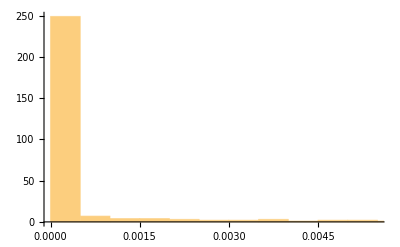

```mathematica
Histogram[%6]
```

```mathematica
Export["Maxwell.txt",%14]
```

Maxwell.txt

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Maxwell.txt"]]]
```

```mathematica
Table[N[CDF[ChiSquareDistribution[38], i]-CDF[ChiSquareDistribution[38], i-1]],{i,321}]
```

{9.75372×10^-24,3.18295×10^-18,4.39144×10^-15,6.43335×10^-13,2.73815×10^-11,5.30807×10^-10,5.96978×10^-9,4.50592×10^-8,2.50875×10^-7,1.09924×10^-6,3.96969×10^-6,0.0000122257,0.0000329515,0.0000793029,0.000173146,0.000347371,0.000647092,0.00112894,0.00185798,0.00290212,0.0043246,0.00617541,0.00848291,0.0112471,0.0144353,0.0179814,0.0217886,0.0257353,0.0296833,0.0334878,0.0370077,0.0401148,0.042702,0.0446887,0.0460244,0.046689,0.046692,0.0460687,0.0448759,0.0431865,0.0410841,0.0386576,0.0359963,0.0331859,0.0303052,0.0274242,0.0246023,0.0218877,0.019318,0.0169199,0.014711,0.0127006,0.0108907,0.0092779,0.0078544,0.00660912,0.00552886,0.00459915,0.003805,0.00313146,0.00256407,0.00208919,0.00169417,0.00136752,0.00109893,0.000879284,0.000700591,0.000555944,0.000439422,0.000345991,0.000271412,0.000212139,0.000165227,0.000128249,0.0000992159,0.0000765064,0.0000588088,0.0000450662,0.0000344316,0.0000262297,0.0000199248,0.0000150934,0.0000114025,8.59146×10^-6,6.45671×10^-6,4.84017×10^-6,3.61943×10^-6,2.70006×10^-6,2.00949×10^-6,1.49211×10^-6,1.10545×10^-6,8.17185×10^-7,6.02794×10^-7,4.43714×10^-7,3.25944×10^-7,2.3895×10^-7,1.74829×10^-7,1.27667×10^-7,9.30517×10^-8,6.76958×10^-8,4.91598×10^-8,3.56355×10^-8,2.57868×10^-8,1.86281×10^-8,1.34341×10^-8,9.67234×10^-9,6.95269×10^-9,4.98981×10^-9,3.57552×10^-9,2.55817×10^-9,1.82754×10^-9,1.30366×10^-9,9.28611×10^-10,6.60518×10^-10,4.69168×10^-10,3.32794×10^-10,2.35741×10^-10,1.66771×10^-10,1.17825×10^-10,8.31381×10^-11,5.85886×10^-11,4.12371×10^-11,2.89889×10^-11,2.03544×10^-11,1.42747×10^-11,9.99945×10^-12,6.99663×10^-12,4.88998×10^-12,3.41382×10^-12,2.38076×10^-12,1.65845×10^-12,1.15419×10^-12,8.02247×10^-13,5.57221×10^-13,3.86469×10^-13,2.67897×10^-13,1.85518×10^-13,1.28342×10^-13,8.85958×10^-14,6.12843×10^-14,4.21885×10^-14,2.90878×10^-14,2.0095×10^-14,1.37668×10^-14,9.4369×10^-15,6.55032×10^-15,4.44089×10^-15,2.9976×10^-15,2.10942×10^-15,1.44329×10^-15,9.99201×10^-16,6.66134×10^-16,4.44089×10^-16,3.33067×10^-16,2.22045×10^-16,1.11022×10^-16,1.11022×10^-16,1.11022×10^-16,0.,0.,1.11022×10^-16,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Export["ChiSquare38.txt",%22]
```

ChiSquare38.txt

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["ChiSquare38.txt"]]]
```

```mathematica
N[CDF[ChiSquareDistribution[319],1290.7836574324556]](* 泊松 *)
N[CDF[ChiSquareDistribution[319],280.18929425914297]](* 麦克斯韦 *)
N[CDF[ChiSquareDistribution[319],805.167803087271]](* 卡方 *)
```

1.

0.0573974

1.

```mathematica
N[∫_0^(+∞) 4 π^-1 N[a]^3 ⅇ^(-N[a]^2 x^2/π)(x/√π)^2 ⅆx]
```

1.

1/a

```mathematica
D[ⅇ^(-b^2 x^2)x^6,x]
```

6 ⅇ^(-b^2 x^2) x^5-2 b^2 ⅇ^(-b^2 x^2) x^7

```mathematica
Simplify[6 ⅇ^(-b^2 x^2) x^5-2 b^2 ⅇ^(-b^2 x^2) x^7]
```

-2 ⅇ^(-b^2 x^2) x^5 (-3+b^2 x^2)

```mathematica
∫_0^(+∞) ⅇ^(-b^2 x^2)x^6 ⅆx
```

ConditionalExpression[(15 √π)/(16 (b^2)^(7/2)),Re[b^2]>0]

```mathematica
a=0.0187062
N[a]
```

0.0187062

0.0187062

```mathematica
b=0.0106
∫_(√(b^-1))^(√(b^-1)+600) 4 π^-0.5 N[b]^3 ⅇ^(-N[b]^2 x^2)x^2 ⅆx
```

0.0106

0.999184

```mathematica
|
```

```mathematica
1.5^(1/2)b^-1/1.411866
```

81.8364

```mathematica
Table[∫_(i-1)^i 4 π^-0.5 N[a]^3 ⅇ^(-N[a]^2 x^2)x^2 ⅆx,{i,320}]
```

{6.00209×10^-7,4.20072×10^-6,0.000011398,0.0000221847,0.0000365496,0.0000544779,0.0000759512,0.000100947,0.00012944,0.000161401,0.000196797,0.000235591,0.000277744,0.000323212,0.000371949,0.000423905,0.000479027,0.000537258,0.00059854,0.000662809,0.000730001,0.000800047,0.000872877,0.000948417,0.00102659,0.00110732,0.00119052,0.00127611,0.00136401,0.00145413,0.00154637,0.00164065,0.00173688,0.00183495,0.00193477,0.00203625,0.00213929,0.00224378,0.00234962,0.00245672,0.00256496,0.00267425,0.00278449,0.00289555,0.00300735,0.00311978,0.00323273,0.00334609,0.00345977,0.00357365,0.00368763,0.00380161,0.00391549,0.00402916,0.00414252,0.00425546,0.0043679,0.00447973,0.00459086,0.00470118,0.00481061,0.00491905,0.00502641,0.00513261,0.00523754,0.00534113,0.0054433,0.00554396,0.00564303,0.00574043,0.0058361,0.00592995,0.00602191,0.00611193,0.00619993,0.00628584,0.00636962,0.0064512,0.00653052,0.00660753,0.00668219,0.00675445,0.00682425,0.00689157,0.00695636,0.00701858,0.0070782,0.0071352,0.00718953,0.00724119,0.00729014,0.00733637,0.00737986,0.00742059,0.00745856,0.00749375,0.00752617,0.0075558,0.00758264,0.00760671,0.007628,0.00764651,0.00766227,0.00767528,0.00768555,0.0076931,0.00769795,0.00770012,0.00769963,0.00769651,0.00769078,0.00768248,0.00767164,0.00765828,0.00764244,0.00762416,0.00760347,0.00758042,0.00755504,0.00752738,0.00749749,0.00746539,0.00743115,0.00739481,0.00735642,0.00731602,0.00727367,0.00722941,0.00718331,0.0071354,0.00708575,0.00703441,0.00698144,0.00692688,0.00687079,0.00681323,0.00675426,0.00669393,0.00663229,0.0065694,0.00650533,0.00644011,0.00637382,0.0063065,0.00623822,0.00616902,0.00609896,0.0060281,0.00595649,0.00588418,0.00581124,0.0057377,0.00566362,0.00558906,0.00551407,0.00543869,0.00536297,0.00528696,0.00521072,0.00513428,0.0050577,0.00498101,0.00490427,0.00482751,0.00475078,0.00467412,0.00459757,0.00452117,0.00444496,0.00436898,0.00429325,0.00421782,0.00414272,0.00406799,0.00399365,0.00391974,0.00384628,0.00377331,0.00370085,0.00362893,0.00355758,0.00348681,0.00341666,0.00334714,0.00327828,0.00321009,0.0031426,0.00307582,0.00300977,0.00294446,0.00287992,0.00281615,0.00275317,0.00269099,0.00262963,0.00256908,0.00250936,0.00245049,0.00239246,0.00233528,0.00227897,0.00222351,0.00216893,0.00211522,0.00206239,0.00201043,0.00195936,0.00190916,0.00185984,0.0018114,0.00176384,0.00171715,0.00167134,0.0016264,0.00158233,0.00153911,0.00149676,0.00145526,0.0014146,0.00137479,0.00133581,0.00129767,0.00126034,0.00122382,0.00118812,0.00115321,0.00111909,0.00108574,0.00105318,0.00102137,0.000990313,0.000960001,0.000930423,0.000901567,0.000873424,0.000845982,0.000819233,0.000793164,0.000767766,0.000743027,0.000718936,0.000695483,0.000672656,0.000650444,0.000628836,0.000607821,0.000587388,0.000567525,0.000548222,0.000529467,0.00051125,0.000493558,0.000476382,0.00045971,0.000443531,0.000427835,0.00041261,0.000397847,0.000383535,0.000369662,0.00035622,0.000343197,0.000330584,0.00031837,0.000306546,0.000295102,0.000284028,0.000273315,0.000262954,0.000252935,0.000243249,0.000233887,0.000224841,0.000216101,0.00020766,0.000199509,0.00019164,0.000184045,0.000176716,0.000169645,0.000162825,0.000156249,0.000149908,0.000143796,0.000137907,0.000132232,0.000126766,0.000121502,0.000116434,0.000111556,0.00010686,0.000102343,0.0000979972,0.0000938177,0.0000897988,0.0000859354,0.0000822221,0.000078654,0.0000752261,0.0000719336,0.0000687718,0.0000657362,0.0000628224,0.0000600261,0.0000573432,0.0000547696,0.0000523014,0.0000499348,0.000047666,0.0000454915,0.0000434079,0.0000414117,0.0000394997,0.0000376687,0.0000359157,0.0000342377,0.0000326318,0.0000310952,0.0000296254,0.0000282195}

```mathematica
Export["Maxwell.txt",%5]
```

Maxwell.txt

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Maxwell4.txt"]]]
```